```mathematica
{log, log2}={NotebookDirectory[]<>"log.txt",NotebookDirectory[]<>"log2.txt"};
```

```mathematica
logD=ReadList[log,{Word, Number, Number}][[All,{2,3}]]
log2D=ReadList[log2,{Word, Number, Number}][[All,{2,3}]]
```

{{3,0},{4,15},{5,16},{6,0},{7,0},{8,16},{9,0},{10,0},{11,0},{12,0},{13,15},{14,0},{15,0},{16,0},{17,16},{18,15},{19,0},{20,0},{21,16},{22,0},{23,0},{24,16},{25,0},{26,0},{27,15},{28,0},{29,16},{30,0},{31,15},{32,0},{33,0},{34,16},{35,0},{36,16},{37,0},{38,15},{39,0},{40,16},{41,15},{42,0},{43,16},{44,16},{45,0},{46,15},{47,0},{48,16},{49,15},{50,16},{51,0},{52,16},{53,15},{54,16},{55,0},{56,15},{57,16},{58,31},{59,16},{60,15},{61,16},{62,16},{63,15},{64,0},{65,16},{66,15},{67,32},{68,15},{69,31},{70,16},{71,16},{72,31},{73,31},{74,31},{75,31},{76,32},{77,31},{78,15},{79,16},{80,31},{81,16},{82,15},{83,47},{84,31},{85,47},{86,16},{87,31},{88,47},{89,15},{90,32},{91,31},{92,31},{93,31},{94,47},{95,31},{96,47},{97,31},{98,31},{99,47},{100,31},{101,32},{102,31},{103,47},{104,31},{105,31},{106,47},{107,47},{108,31},{109,47},{110,46},{111,47},{112,47},{113,47},{114,47},{115,46},{116,32},{117,62},{118,78},{119,47},{120,78},{121,47},{122,46},{123,63},{124,62},{125,47},{126,47},{127,62},{128,47},{129,62},{130,63},{131,47},{132,93},{133,63},{134,93},{135,78},{136,63},{137,78},{138,62},{139,78},{140,78},{141,78},{142,78},{143,62},{144,94},{145,109},{146,78},{147,94},{148,78},{149,78},{150,93},{151,78},{152,78},{153,78},{154,110},{155,109},{156,109},{157,78},{158,78},{159,94},{160,78},{161,93},{162,109},{163,94},{164,94},{165,109},{166,93},{167,110},{168,109},{169,125},{170,124},{171,110},{172,93},{173,109},{174,110},{175,109},{176,125},{177,156},{178,140},{179,94},{180,124},{181,125},{182,156},{183,125},{184,156},{185,203},{186,109},{187,140},{188,125},{189,125},{190,156},{191,125},{192,125},{193,140},{194,140},{195,141},{196,171},{197,156},{198,141},{199,156},{200,171}}

{{3,0},{4,16},{5,5},{6,4},{7,2},{8,7},{9,5},{10,3},{11,2},{12,4},{13,8},{14,14},{15,5},{16,4},{17,8},{18,9},{19,9},{20,7},{21,8},{22,9},{23,11},{24,17},{25,9},{26,12},{27,12},{28,15},{29,14},{30,16},{31,17},{32,18},{33,21},{34,19},{35,20},{36,21},{37,26},{38,22},{39,28},{40,31},{41,33},{42,33},{43,34},{44,33},{45,35},{46,39},{47,38},{48,41},{49,44},{50,43},{51,42},{52,49},{53,46},{54,47},{55,53},{56,76},{57,75},{58,94},{59,80},{60,138},{61,90},{62,88},{63,98},{64,109},{65,118},{66,77},{67,74},{68,76},{69,92},{70,91},{71,109},{72,114},{73,93},{74,101},{75,101},{76,110},{77,102},{78,102},{79,111},{80,110},{81,114},{82,118},{83,120},{84,121},{85,125},{86,134},{87,130},{88,137},{89,139},{90,140},{91,140},{92,154},{93,153},{94,153},{95,158},{96,161},{97,162},{98,163},{99,173},{100,176},{101,176},{102,188},{103,189},{104,194},{105,196},{106,182},{107,199},{108,206},{109,203},{110,219},{111,218},{112,235},{113,226},{114,232},{115,253},{116,234},{117,248},{118,257},{119,286},{120,258},{121,270},{122,280},{123,270},{124,288},{125,279},{126,296},{127,300},{128,307},{129,314},{130,309},{131,307},{132,311},{133,325},{134,331},{135,333},{136,326},{137,343},{138,339},{139,358},{140,363},{141,369},{142,358},{143,353},{144,368},{145,380},{146,405},{147,402},{148,417},{149,403},{150,423},{151,421},{152,431},{153,450},{154,438},{155,419},{156,428},{157,416},{158,443},{159,444},{160,451},{161,450},{162,534},{163,463},{164,474},{165,591},{166,546},{167,631},{168,523},{169,507},{170,543},{171,519},{172,506},{173,511},{174,538},{175,540},{176,549},{177,557},{178,608},{179,583},{180,572},{181,618},{182,562},{183,581},{184,609},{185,595},{186,600},{187,629},{188,643},{189,635},{190,627},{191,678},{192,673},{193,684},{194,630},{195,669},{196,690},{197,686},{198,686},{199,683},{200,692}}

```mathematica
m=First[logD][[1]];
M=Last[logD][[1]];
```

```mathematica
logFitL=Fit[logD, {1,x},x]
Total[Abs[(logFitL/.x->#[[1]])-#[[2]]]&/@logD]
logFitSq=Fit[logD, {1,x^2},x]
Total[Abs[(logFitSq/.x->#[[1]])-#[[2]]]&/@logD]
```

-23.9339+0.764389 x

2725.27

2.0976+0.00379934 x^2

1827.29

```mathematica
log2FitL=Fit[log2D, {1,x},x]
Total[Abs[(log2FitL/.x->#[[1]])-#[[2]]]&/@log2D]
log2FitSq=Fit[log2D, {1,x^2},x]
Total[Abs[(log2FitSq/.x->#[[1]])-#[[2]]]&/@log2D]
```

-122.08+3.63346 x

8983.78

4.29071+0.017866 x^2

2240.73

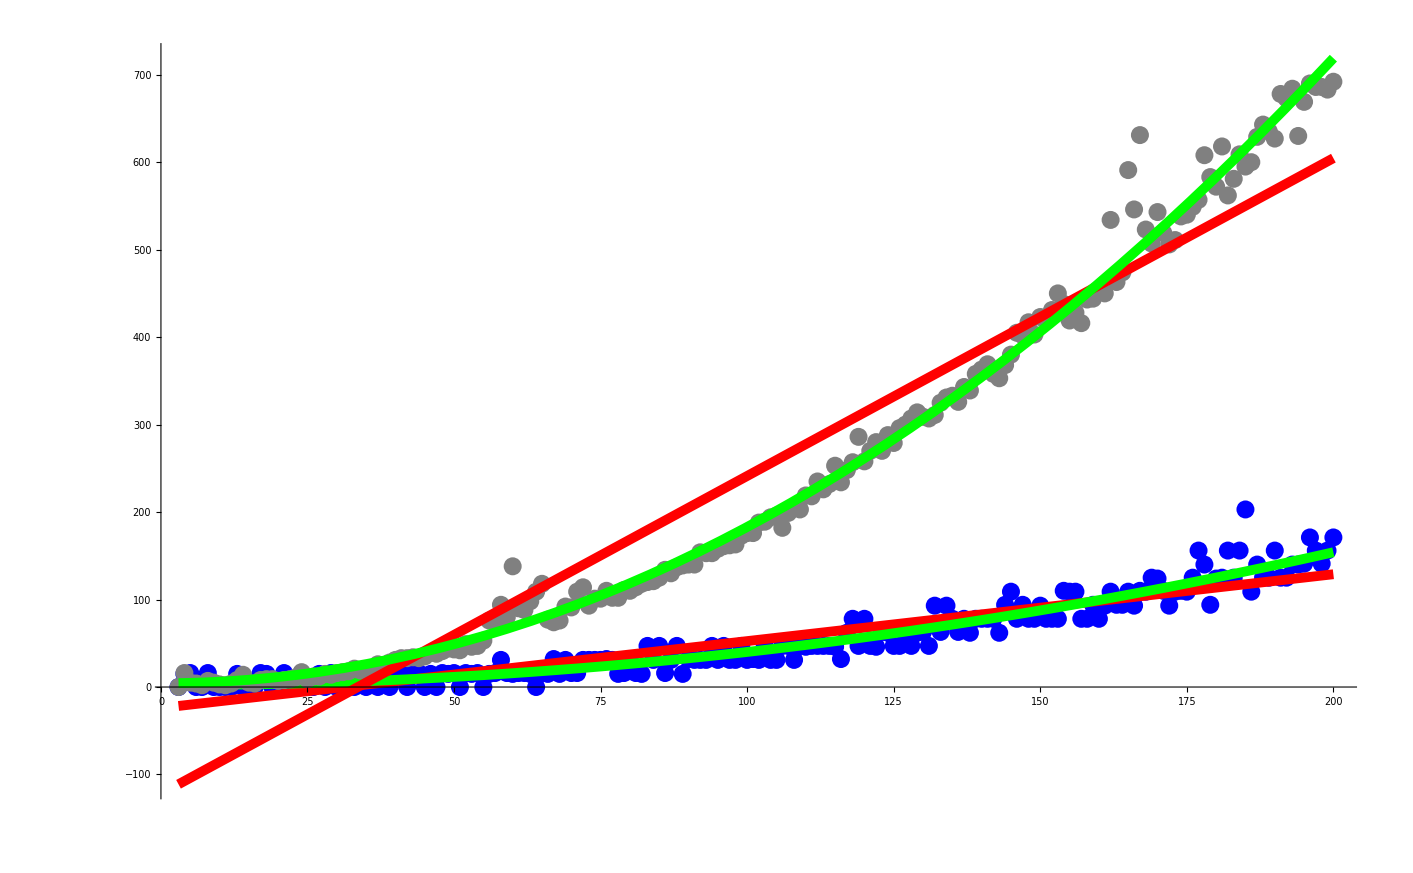

```mathematica
Show[
ListPlot[logD, PlotStyle->Blue],
Plot[logFitL,{x,m, M},PlotStyle->{Red,  Thickness[0.005]}],
Plot[logFitSq,{x,m, M},PlotStyle->{Green, Thickness[0.005]}],

ListPlot[log2D, PlotStyle->Gray],
Plot[log2FitL,{x,m, M},PlotStyle->{Red,  Thickness[0.005]}],
Plot[log2FitSq,{x,m, M},PlotStyle->{Green, Thickness[0.005]}],
PlotRange->All
]
```

{{4,2.75},{5,3.},{8,3.25},{130,11.832},{15,4.33},{18,4.56},{20,5.2},{23,3.91},{25,4.92},{840,25.7049}}

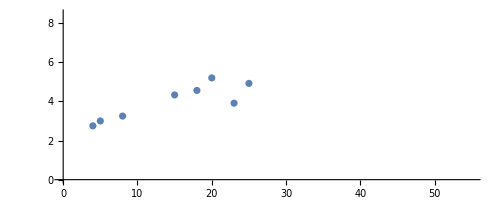

```mathematica
data2={{4,2.75},{5,3.00},{8,3.25},{10,2.90}{13,4.08},{15,4.33},{18,4.56},{20,5.20},{23,3.91},{25,4.92},{28,5.07}{30,5.07}}
ListPlot[data2,AspectRatio->Automatic]
```